Menyelesaikan persamaan TOV secara numerik

Referensi: 
(http://kugelblitzblackholes.wordpress.com/2015/02/07/numerical-work-in-general-relativity-4-tov-equations/ diakses 25-Juli-2016, pukul 14:38) 
Kodingan Icang

Kode berikut hanya untuk memplot sebuah profil

EOS QUARK Matter based on Extended CIDDM parameter set 
with DI-2500, D1 = 0.46, D2 = 0.3
Energy density as a function of pressure
unit MeV fm^(-3)

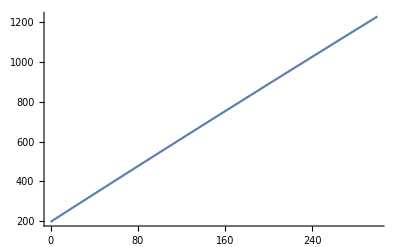

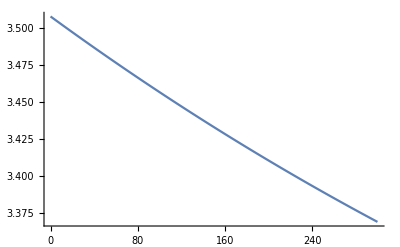

```mathematica
ϵ[p_]=(197.282+3.50745 p-0.000267588 p^2+8.79024*10^-8 p^3-1.38896*10^-11 p^4+8.28846*10^-16 p^5); (* Model Quark Star *)
dϵdp=D[ϵ[p],p];
Plot[ϵ[p],{p,0,300}]
Plot[dϵdp,{p,0,300}]
```

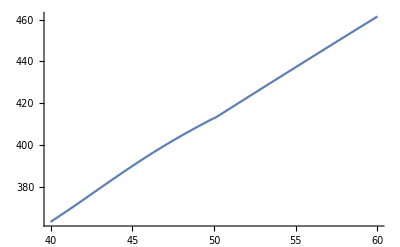

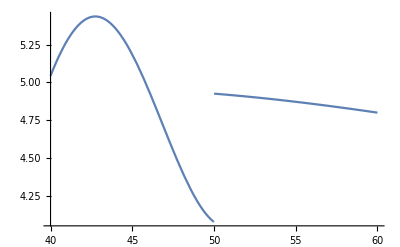

```mathematica
(* Model Neutron Star *)
FED1[P0_]=198.44659150368602+2.1700464559579813*P0+0.088730114353849*P0^2-0.00136997852494318*P0^3+0.000011358780185274*P0^4-5.97851057883043*10^(-8)*P0^5+2.1189092442107564*10^(-10)*P0^6-5.17833315779507*10^(-13)*P0^7+8.747685021941607*10^(-16)*P0^8-1.003326088565395*10^(-18)*P0^9+7.457832417744333*10^(-22)*P0^10-3.240190924875843*10^(-25)*P0^11+6.246104864722871*10^(-29)*P0^12;
FED2[P0_]=31.709610100869888+90.64073102501017*P0-29.153519698621*P0^2+5.4623392991109*P0^3-0.59924819745741*P0^4+0.041227991444036*P0^5-0.00186278195081703*P0^6+0.0000566704237195*P0^7-1.1680183124666673*10^(-6)*P0^8+1.6078512679724317*10^(-8)*P0^9-1.4153078467797958*10^(-10)*P0^10+7.20266639116908*10^(-13)*P0^11-1.6117637094790372*10^(-15)*P0^12;
FED3[P0_]=((P0-3.364*10^(-4))/(1.006*10^(-3)))^(3/4);
FED4[P0_]=7.405868060399274*10^(-4)+714.60658392886*P0-1.1556601395474602*10^(6)*P0^2+2.365618005585925*10^(9)*P0^3-1.752008202465829*10^(12)*P0^4;
ϵ[p_]=
Piecewise[{{FED1[p],p>50.},{FED2[p],0.274<p≤50.},{FED3[p],4.99313436*10^(-4)<p≤0.274}},FED4[p]]; (* Model Neutron Star *)
dϵdp=D[ϵ[p],p];
Plot[ϵ[p],{p,40,60}]
Plot[dϵdp,{p,40,60}]
```

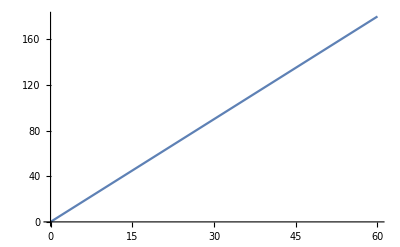

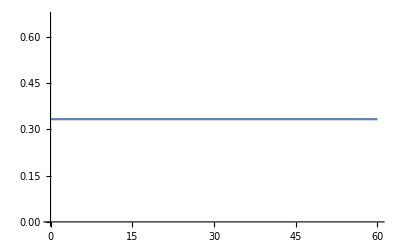

```mathematica
ϵ[p_]=p/w+ϵk;
w=1/3;
ϵk=240.;
dϵdp=D[ϵ[p],p];
Plot[ϵ[p],{p,0,60}]
Plot[1/dϵdp,{p,0,60}]
```

```mathematica
(* Model LinEoS *)
ϵ[p_]=
p/1.+197.282; 
dϵdp=D[ϵ[p],p];
(* Model LinEoS *)
```

```mathematica
(* Model densitas energi konstan *)
ϵ[p_]=
240.; 
dϵdp=D[ϵ[p],p];
(* Model LinEoS *)
```

```mathematica
eq1[r_]=(4 π r^3 p[r]+m[r])(2GS)/(2 r (r-2 GS m[r]));
(*Persamaan differensial metrik*)
eq2[r_]=-m'[r]+4 π r^2 ϵ[p[r]];(*Persamaan differensial massa*)
eq3[r_]=-p'[r]- eq1[r](ϵ[p[r]]+p[r]) ; (*Persamaan TOV*)
```

```mathematica
GS=1.325*10^-12; (* Konstanta gravitasi *)
MSS= 1.1155 * 10^15; (* Massa matahari *)
r0=10^(-3);(* radius di pusat *)
rmax=100000.;
MCC=1 *10^-9; (* Massa di pusat *)
PCC=300; (* Tekanan di pusat *)
```

```mathematica
Clear[rStar];
state=First[NDSolve`ProcessEquations[{eq2[r]==0,eq3[r]==0,m[r0]==MCC , p[r0]==PCC},{m,p},{r,r0,rmax},Method->{"EventLocator","Event" :>{p[r]},"EventAction":>Throw[rStar=r,"StopIntegration"]}]];
NDSolve`Iterate[state,rmax]
sol=NDSolve`ProcessSolutions[state]
rStar
```

{m→InterpolatingFunction[{{0.001, 17062.9}}, <>],p→InterpolatingFunction[{{0.001, 17062.9}}, <>]}

17062.9

17062.88829323245     4.477008501499378     240.     300

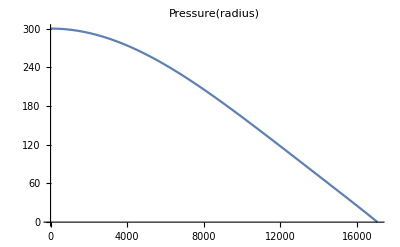

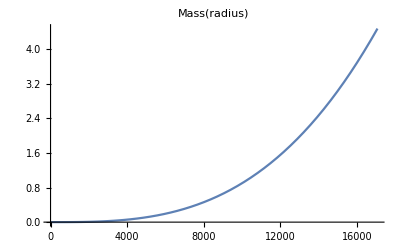

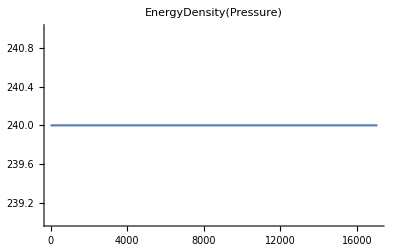

```mathematica
mo[r_]=Evaluate[m[r]/. sol];
po[r_]=Evaluate[p[r]/. sol];
mStar=mo[rStar];
(*Print[rStar,"     ",mStar/MSS,"     ",ϵ[p[r0]],"     ",PCC]*)
Print[FortranForm[rStar],"     ",FortranForm[mo[rStar]/MSS],"     ",ϵ[po[r0]],"     ",PCC]
Plot[{po[r]},{r,r0,rStar},PlotRange->All,PlotLabel->Pressure[radius]]
Plot[{mo[r]/MSS},{r,r0,rStar},PlotRange->All,PlotLabel->Mass[radius]]
Plot[{ϵ[po[r]]},{r,r0,rStar},PlotRange->All,PlotLabel->EnergyDensity[Pressure]]
```

```mathematica
{rStar,mo[rStar],po[rStar]}
{r0,po[r0],mo[r0]}
{1-2GS mo[rStar]/rStar}
```

{17062.9,4.9941×10^15,3.06422×10^-14}

{1/1000,300.,1.×10^-9}

{0.224377}